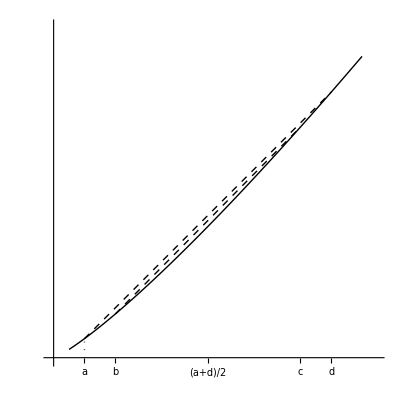

```mathematica
f[t_,u_]:=t^u;

f1=Plot[f[t,1.2],{t,1,20},PlotStyle->{Black,Thickness[0.0025]}];
line1=Plot[(f[18,1.2]-f[2,1.2])/(18-2)*(t-2)+f[2,1.2],{t,2,18},PlotStyle->{Black,Dashed}];
line2=Plot[(f[16,1.2]-f[4,1.2])/(16-4)*(t-4)+f[4,1.2],{t,4,16},PlotStyle->{Black,Dashed}];

oline1=ParametricPlot[{2,t},{t,0,f[2,1.2]}, PlotStyle->{Black,Dotted}];



Show[f1,line1,line2,oline1,Ticks->{ {{2,a},{4,b},{16,c},{18,d},{10,(a+d)/2}},None},LabelStyle->{36},PlotRange->{{-.2,21},{-0.2,40}},Axes->True,AspectRatio->1,AxesOrigin->{0,0},AxesStyle->Arrowheads[{0.0,0.03}]]
```